## Ecuaciones no lineales. Resolución numérica (11-12-17)

Resultado conocido:
Teorema de Bolzano. Si f es una función continua en un intervalo [a,b] y f toma signos opuestos en los extremos (f(a)f(b)<0), existe un punto c en (a,b) tal que f(c)=0.
Bajo ciertas condiciones, se garantiza la existencia de solución de la ecuación f(x)=0.
Método de bisección: 
En las condiciones del Teorema de Bolzano, el método de bisección consiste en reducir el intervalo (manteniendo el cambio de signo) dividiéndolo por la mitad en cada paso.

```mathematica
f[x_]:=x^2-2
```

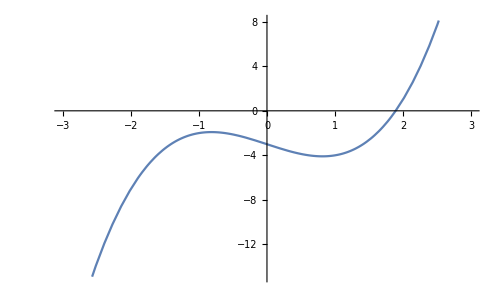

```mathematica
Plot[f[x],{x,-3,3}]
```

```mathematica
a=1;b=2;If[f[a]f[b]<0,Do[If[f[(a+b)/2]f[a]>0,a=(a+b)/2,b=(a+b)/2],{20}];Print["La solución está entre ",N[a,10]," y ",N[b,10],". Una aproximación sería ",N[(a+b)/2,10],". La función vale ",N[f[(a+b)/2],10]],
Print["No hay cambio de signo. Cambia los puntos."]];
```

Hay varias posibilidades de parada, además del número de iteraciones; Amplitud del intervalo (“cifras exactas”), valor de la función, ... Individualmente, o combinadas.

Método de Regula-Falsi, consiste en tomar un valor intermedio dependiendo de los valores de la función en los extremos (más cerca del extremo donde la función esté más próxima a cero).

Sería decir que el punto intermedio, en lugar de ser (a+b)/2, sea un x tal que (x-a)/(f(a))=(x-b)/(f(b)), despejando, x = (a f(b)-b f(a))/(f(b)-f(a)). Posteriormente, nos quedaremos con el trozo [a,x] o [x,b]  donde se produzca el cambio de signo de la función.

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x^2-2
```

```mathematica
a=0;b=3;If[f[a]f[b]<0,Do[If[f[(a f[b]-b f[a])/(f[b]-f[a])]f[a]>0,a=(a f[b]-b f[a])/(f[b]-f[a]),b=(a f[b]-b f[a])/(f[b]-f[a])],{20}];Print["La solución está entre ",N[a,10]," y ",N[b,10],". Una aproximación sería ",N[(a f[b]-b f[a])/(f[b]-f[a]),10],". La función vale ",N[f[(a f[b]-b f[a])/(f[b]-f[a])],10]],
Print["No hay cambio de signo. Cambia los puntos."]];
```

La solución está entre 1.414213559 y 3.. Una aproximación sería 1.414213561. La función vale -3.683905784×10^-9

Este método de dividir el intervalo proporcionalmente a los valores en los extremos es equivalente a considerar el segmento (o la recta) que pasa por los puntos (a,f(a)) y (b,f(b)), y considerar el punto donde esta recta vale cero.

La recta que pasa por los puntos (a,f(a)) y (b,f(b)) es y= f(a) + (f(b)-f(a))/(b-a)(x-a). Cuando y es 0, f(a) + (f(b)-f(a))/(b-a)(x-a)=0, entonces, (f(b)-f(a))/(b-a)(x-a)=-f(a), (x-a)=(- f(a))/((f(b)-f(a))/(b-a)), x=a - (f(a))/((f(b)-f(a))/(b-a)) = a - (f(a) (b-a))/(f(b)-f(a)) = (a f(b) -b f(a))/(f(b)-f(a)).

Usualmente, el método de Regula Falsi acaba por dejar fijo uno de los extremos del intervalo y sólo mueve el otro. Esto ralentiza el método. Podríamos considerar el método sin imponer el cambio de signo, sólo considerar a partir de dos puntos, la recta que los une y el punto de corte. Se trataría del método de la secante.

x_0= a, x_1=b, ..., x_(n+2)=(x_n f(x_(n+1))-x_(n+1) f(x_n))/(f(x_(n+1))-f(x_n))

En realidad, no sería necesario que haya cambio de signo de la función en los puntos a y b.

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x^2-2
```

EL PROBLEMA DE ESTE METODO ES QUE SI NO TIENE SOLUCION SE VA A BLOQUEAR PORQUE NO PUEDE DAR NINGUN VALOR. EN CAMBIO, CON LA BISECCION SI NO HAY SOLUCION SE INDICA.

```mathematica
a=12;b=3;Do[c=b; b=(a f[b]-b f[a])/(f[b]-f[a]); a=c,{20}];Print["Una aproximación sería ",N[b,10],". La función vale ",N[f[b],10]]
```

Una aproximación sería 1.414213562. La función vale 3.091528292×10^-5562

Otra posibilidad es considerar en lugar de la recta que pasa por dos puntos de la gráfica, la recta tangente a ésta en un punto. 

Dada una aproximación inicial x_0, la recta tangente en (x_0, f(x_0)) sería y=f(x_0) + f ’(x_0) (x-x_0), que se anula en el punto 

			x_1 = x_0 - (f(x_0))/(f'(x_0))

En general, podemos construir la sucesión 

			x_(n+1) = x_n - (f(x_n))/(f'(x_n))
Se trata del método de Newton.

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x^5+7*x^4 - 7 * x^3 + 4 * x^2 -3 x - 5;
```

```mathematica
x=16.0;
Do[x=x-f[x]/f'[x];Print[N[x,15]],{10}];Print["Una aproximación sería ",N[x,10],". La función vale ",N[f[x],10]]
```

12.615

9.92397

7.78959

6.10176

4.77196

3.72899

2.91589

2.28792

1.81207

1.46826

Una aproximación sería 1.46826. La función vale 16.4173